```mathematica
k[n_,T_] = (2 π ⅈ n)/T
λ[n_,m_,l_,T_] =  (π/l)^2 m^2+(2π ⅈ)/T n
```

(2 ⅈ n π)/T

(m^2 π^2)/l^2+(2 ⅈ n π)/T

```mathematica
u[x_,t_,T_,l_,n_,m_] = Exp[k[n,T]*t]Sinh[Sqrt[k[n,T]-λ[n,m,l,T]]*x]
```

ⅇ^((2 ⅈ n π t)/T) Sinh[√(-m^2/l^2) π x]

```mathematica
Tval =  1
lval = 1
nval=1
mval=1
```

1

1

1

«1 more identical outputs»

```mathematica
u[x,t,Tval,lval,nval,mval]
```

ⅈ ⅇ^(2 ⅈ π t) Sin[π x]

```mathematica
Plot3D[Re[u[x,t, Tval,lval,nval,mval]],{x,0,lval},{t,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[Im[u[x,t, Tval,lval,nval,mval]],{x,0,lval},{t,0,1},PlotRange->{-1,1}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Re[u[x,t, Tval,lval,nval,mval]],{x,0,lval},PlotRange->{-2,2}],{t,0,Tval}]
```

```mathematica
Manipulate[Plot[Im[u[x,t, Tval,lval,nval,mval]],{x,0,lval},PlotRange->{-1,1}],{t,0,Tval}]
```

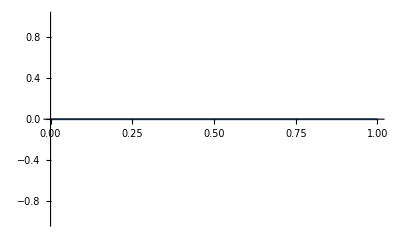

```mathematica
Plot[Im[λ[m,1,1,1]],{m,0,1}]
```

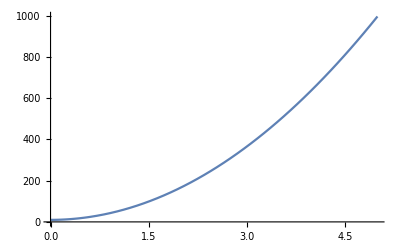

```mathematica
Plot[Re[λ[m,1,1,1]],{m,0,5}]
```

```mathematica
λ[3,3,1,1]
```

18 π-9 π^2